# Bistable motif: parameter sampling

## Finding the condition of multistationarity

We consider the following reactions:

K+S⇋KS→K+S_p
K^✶+S⇋K^✶S→K^✶+S_p
S_p→S
K⇋K^✶
KS⇋K^✶S

The species of the system are:

{S,S_p,K,K^✶,KS,K^✶S}

In total, there are 11 reations and 6 species.

We firstly construct the ordinary differential equations based on mass-action kinetics. Then compute the determinant of Jacobian, using the solution at critical point (steady state) to calculate the determinant. The (necessary) condition for multistationarity is to make determinant equal to zero (non-zero determinant implys injectivity).

```mathematica
ClearAll["Global`*"];
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={k[1]×x[3]×x[1],k[2]×x[5],k[3]×x[5],k[4]×x[4]×x[1],k[5]×x[6],k[6]×x[6],k[7]×x[2],k[8]×x[3],k[9]×x[4],k[10]×x[5],k[11]×x[6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
cons={x[1]+x[2]+x[5]+x[6]-T[1],x[3]+x[4]+x[5]+x[6]-T[2]};
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],x[1]+x[2]+x[5]+x[6]-T[1],x[3]+x[4]+x[5]+x[6]-T[2]};
jacobian=D[subsEqns,{{x[1],x[2],x[3],x[4],x[5],x[6]}}];
detJ=Collect[Distribute[Det[jacobian]],{x[1],x[2],x[3],x[4],x[5],x[6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{x[2],x[4],x[5],x[6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],x[_],FactorTerms]
```

-k[2]^2 k[5]^2 k[7] k[8] k[9]-2 k[2] k[3] k[5]^2 k[7] k[8] k[9]-k[3]^2 k[5]^2 k[7] k[8] k[9]-2 k[2]^2 k[5] k[6] k[7] k[8] k[9]-4 k[2] k[3] k[5] k[6] k[7] k[8] k[9]-2 k[3]^2 k[5] k[6] k[7] k[8] k[9]-k[2]^2 k[6]^2 k[7] k[8] k[9]-2 k[2] k[3] k[6]^2 k[7] k[8] k[9]-k[3]^2 k[6]^2 k[7] k[8] k[9]-k[2]^2 k[5]^2 k[7] k[9]^2-2 k[2] k[3] k[5]^2 k[7] k[9]^2-k[3]^2 k[5]^2 k[7] k[9]^2-2 k[2]^2 k[5] k[6] k[7] k[9]^2-4 k[2] k[3] k[5] k[6] k[7] k[9]^2-2 k[3]^2 k[5] k[6] k[7] k[9]^2-k[2]^2 k[6]^2 k[7] k[9]^2-2 k[2] k[3] k[6]^2 k[7] k[9]^2-k[3]^2 k[6]^2 k[7] k[9]^2-2 k[2] k[5]^2 k[7] k[8] k[9] k[10]-2 k[3] k[5]^2 k[7] k[8] k[9] k[10]-4 k[2] k[5] k[6] k[7] k[8] k[9] k[10]-4 k[3] k[5] k[6] k[7] k[8] k[9] k[10]-2 k[2] k[6]^2 k[7] k[8] k[9] k[10]-2 k[3] k[6]^2 k[7] k[8] k[9] k[10]-2 k[2] k[5]^2 k[7] k[9]^2 k[10]-2 k[3] k[5]^2 k[7] k[9]^2 k[10]-4 k[2] k[5] k[6] k[7] k[9]^2 k[10]-4 k[3] k[5] k[6] k[7] k[9]^2 k[10]-2 k[2] k[6]^2 k[7] k[9]^2 k[10]-2 k[3] k[6]^2 k[7] k[9]^2 k[10]-k[5]^2 k[7] k[8] k[9] k[10]^2-2 k[5] k[6] k[7] k[8] k[9] k[10]^2-k[6]^2 k[7] k[8] k[9] k[10]^2-k[5]^2 k[7] k[9]^2 k[10]^2-2 k[5] k[6] k[7] k[9]^2 k[10]^2-k[6]^2 k[7] k[9]^2 k[10]^2-2 k[2]^2 k[5] k[7] k[8] k[9] k[11]-4 k[2] k[3] k[5] k[7] k[8] k[9] k[11]-2 k[3]^2 k[5] k[7] k[8] k[9] k[11]-2 k[2]^2 k[6] k[7] k[8] k[9] k[11]-4 k[2] k[3] k[6] k[7] k[8] k[9] k[11]-2 k[3]^2 k[6] k[7] k[8] k[9] k[11]-2 k[2]^2 k[5] k[7] k[9]^2 k[11]-4 k[2] k[3] k[5] k[7] k[9]^2 k[11]-2 k[3]^2 k[5] k[7] k[9]^2 k[11]-2 k[2]^2 k[6] k[7] k[9]^2 k[11]-4 k[2] k[3] k[6] k[7] k[9]^2 k[11]-2 k[3]^2 k[6] k[7] k[9]^2 k[11]-2 k[2] k[5] k[7] k[8] k[9] k[10] k[11]-2 k[3] k[5] k[7] k[8] k[9] k[10] k[11]-2 k[2] k[6] k[7] k[8] k[9] k[10] k[11]-2 k[3] k[6] k[7] k[8] k[9] k[10] k[11]-2 k[2] k[5] k[7] k[9]^2 k[10] k[11]-2 k[3] k[5] k[7] k[9]^2 k[10] k[11]-2 k[2] k[6] k[7] k[9]^2 k[10] k[11]-2 k[3] k[6] k[7] k[9]^2 k[10] k[11]-k[2]^2 k[7] k[8] k[9] k[11]^2-2 k[2] k[3] k[7] k[8] k[9] k[11]^2-k[3]^2 k[7] k[8] k[9] k[11]^2-k[2]^2 k[7] k[9]^2 k[11]^2-2 k[2] k[3] k[7] k[9]^2 k[11]^2-k[3]^2 k[7] k[9]^2 k[11]^2+(-k[1] k[2] k[4]^2 k[7] k[10] k[11]-k[1] k[3] k[4]^2 k[7] k[10] k[11]-k[1] k[2] k[4]^2 k[7] k[11]^2-k[1] k[3] k[4]^2 k[7] k[11]^2) x[1]^3+(-k[2]^2 k[4] k[5] k[6] k[8]^2-2 k[2] k[3] k[4] k[5] k[6] k[8]^2-k[3]^2 k[4] k[5] k[6] k[8]^2-k[2]^2 k[4] k[6]^2 k[8]^2-2 k[2] k[3] k[4] k[6]^2 k[8]^2-k[3]^2 k[4] k[6]^2 k[8]^2-k[2]^2 k[4] k[5] k[7] k[8]^2-2 k[2] k[3] k[4] k[5] k[7] k[8]^2-k[3]^2 k[4] k[5] k[7] k[8]^2-k[2]^2 k[4] k[6] k[7] k[8]^2-2 k[2] k[3] k[4] k[6] k[7] k[8]^2-k[3]^2 k[4] k[6] k[7] k[8]^2-k[1] k[2] k[3] k[5]^2 k[8] k[9]-k[1] k[3]^2 k[5]^2 k[8] k[9]-2 k[1] k[2] k[3] k[5] k[6] k[8] k[9]-2 k[1] k[3]^2 k[5] k[6] k[8] k[9]-k[2]^2 k[4] k[5] k[6] k[8] k[9]-2 k[2] k[3] k[4] k[5] k[6] k[8] k[9]-k[3]^2 k[4] k[5] k[6] k[8] k[9]-k[1] k[2] k[3] k[6]^2 k[8] k[9]-k[1] k[3]^2 k[6]^2 k[8] k[9]-k[2]^2 k[4] k[6]^2 k[8] k[9]-2 k[2] k[3] k[4] k[6]^2 k[8] k[9]-k[3]^2 k[4] k[6]^2 k[8] k[9]-k[2]^2 k[4] k[5] k[7] k[8] k[9]-2 k[2] k[3] k[4] k[5] k[7] k[8] k[9]-k[3]^2 k[4] k[5] k[7] k[8] k[9]-k[1] k[2] k[5]^2 k[7] k[8] k[9]-k[1] k[3] k[5]^2 k[7] k[8] k[9]-k[2]^2 k[4] k[6] k[7] k[8] k[9]-2 k[2] k[3] k[4] k[6] k[7] k[8] k[9]-k[3]^2 k[4] k[6] k[7] k[8] k[9]-2 k[1] k[2] k[5] k[6] k[7] k[8] k[9]-2 k[1] k[3] k[5] k[6] k[7] k[8] k[9]-k[1] k[2] k[6]^2 k[7] k[8] k[9]-k[1] k[3] k[6]^2 k[7] k[8] k[9]-k[1] k[2] k[3] k[5]^2 k[9]^2-k[1] k[3]^2 k[5]^2 k[9]^2-2 k[1] k[2] k[3] k[5] k[6] k[9]^2-2 k[1] k[3]^2 k[5] k[6] k[9]^2-k[1] k[2] k[3] k[6]^2 k[9]^2-k[1] k[3]^2 k[6]^2 k[9]^2-k[1] k[2] k[5]^2 k[7] k[9]^2-k[1] k[3] k[5]^2 k[7] k[9]^2-2 k[1] k[2] k[5] k[6] k[7] k[9]^2-2 k[1] k[3] k[5] k[6] k[7] k[9]^2-k[1] k[2] k[6]^2 k[7] k[9]^2-k[1] k[3] k[6]^2 k[7] k[9]^2-2 k[2] k[4] k[5] k[6] k[8]^2 k[10]-2 k[3] k[4] k[5] k[6] k[8]^2 k[10]-2 k[2] k[4] k[6]^2 k[8]^2 k[10]-2 k[3] k[4] k[6]^2 k[8]^2 k[10]-2 k[2] k[4] k[5] k[7] k[8]^2 k[10]-2 k[3] k[4] k[5] k[7] k[8]^2 k[10]-2 k[2] k[4] k[6] k[7] k[8]^2 k[10]-2 k[3] k[4] k[6] k[7] k[8]^2 k[10]-k[1] k[3] k[5]^2 k[8] k[9] k[10]-k[1] k[2] k[5] k[6] k[8] k[9] k[10]-3 k[1] k[3] k[5] k[6] k[8] k[9] k[10]-2 k[2] k[4] k[5] k[6] k[8] k[9] k[10]-2 k[3] k[4] k[5] k[6] k[8] k[9] k[10]-k[1] k[2] k[6]^2 k[8] k[9] k[10]-2 k[1] k[3] k[6]^2 k[8] k[9] k[10]-2 k[2] k[4] k[6]^2 k[8] k[9] k[10]-2 k[3] k[4] k[6]^2 k[8] k[9] k[10]-k[1] k[2] k[5] k[7] k[8] k[9] k[10]-k[1] k[3] k[5] k[7] k[8] k[9] k[10]-2 k[2] k[4] k[5] k[7] k[8] k[9] k[10]-2 k[3] k[4] k[5] k[7] k[8] k[9] k[10]-k[1] k[5]^2 k[7] k[8] k[9] k[10]-k[1] k[2] k[6] k[7] k[8] k[9] k[10]-k[1] k[3] k[6] k[7] k[8] k[9] k[10]-2 k[2] k[4] k[6] k[7] k[8] k[9] k[10]-2 k[3] k[4] k[6] k[7] k[8] k[9] k[10]-2 k[1] k[5] k[6] k[7] k[8] k[9] k[10]-k[1] k[6]^2 k[7] k[8] k[9] k[10]-k[1] k[3] k[5]^2 k[9]^2 k[10]-k[1] k[2] k[5] k[6] k[9]^2 k[10]-3 k[1] k[3] k[5] k[6] k[9]^2 k[10]-k[1] k[2] k[6]^2 k[9]^2 k[10]-2 k[1] k[3] k[6]^2 k[9]^2 k[10]-k[1] k[2] k[5] k[7] k[9]^2 k[10]-k[1] k[3] k[5] k[7] k[9]^2 k[10]-k[1] k[5]^2 k[7] k[9]^2 k[10]-k[1] k[2] k[6] k[7] k[9]^2 k[10]-k[1] k[3] k[6] k[7] k[9]^2 k[10]-2 k[1] k[5] k[6] k[7] k[9]^2 k[10]-k[1] k[6]^2 k[7] k[9]^2 k[10]-k[4] k[5] k[6] k[8]^2 k[10]^2-k[4] k[6]^2 k[8]^2 k[10]^2-k[4] k[5] k[7] k[8]^2 k[10]^2-k[4] k[6] k[7] k[8]^2 k[10]^2-k[1] k[5] k[6] k[8] k[9] k[10]^2-k[4] k[5] k[6] k[8] k[9] k[10]^2-k[1] k[6]^2 k[8] k[9] k[10]^2-k[4] k[6]^2 k[8] k[9] k[10]^2-k[1] k[5] k[7] k[8] k[9] k[10]^2-k[4] k[5] k[7] k[8] k[9] k[10]^2-k[1] k[6] k[7] k[8] k[9] k[10]^2-k[4] k[6] k[7] k[8] k[9] k[10]^2-k[1] k[5] k[6] k[9]^2 k[10]^2-k[1] k[6]^2 k[9]^2 k[10]^2-k[1] k[5] k[7] k[9]^2 k[10]^2-k[1] k[6] k[7] k[9]^2 k[10]^2-k[2] k[3] k[4] k[5] k[8]^2 k[11]-k[3]^2 k[4] k[5] k[8]^2 k[11]-k[2]^2 k[4] k[6] k[8]^2 k[11]-3 k[2] k[3] k[4] k[6] k[8]^2 k[11]-2 k[3]^2 k[4] k[6] k[8]^2 k[11]-k[2]^2 k[4] k[7] k[8]^2 k[11]-2 k[2] k[3] k[4] k[7] k[8]^2 k[11]-k[3]^2 k[4] k[7] k[8]^2 k[11]-k[2] k[4] k[5] k[7] k[8]^2 k[11]-k[3] k[4] k[5] k[7] k[8]^2 k[11]-k[2] k[4] k[6] k[7] k[8]^2 k[11]-k[3] k[4] k[6] k[7] k[8]^2 k[11]-2 k[1] k[2] k[3] k[5] k[8] k[9] k[11]-2 k[1] k[3]^2 k[5] k[8] k[9] k[11]-k[2] k[3] k[4] k[5] k[8] k[9] k[11]-k[3]^2 k[4] k[5] k[8] k[9] k[11]-2 k[1] k[2] k[3] k[6] k[8] k[9] k[11]-2 k[1] k[3]^2 k[6] k[8] k[9] k[11]-k[2]^2 k[4] k[6] k[8] k[9] k[11]-3 k[2] k[3] k[4] k[6] k[8] k[9] k[11]-2 k[3]^2 k[4] k[6] k[8] k[9] k[11]-k[2]^2 k[4] k[7] k[8] k[9] k[11]-2 k[2] k[3] k[4] k[7] k[8] k[9] k[11]-k[3]^2 k[4] k[7] k[8] k[9] k[11]-2 k[1] k[2] k[5] k[7] k[8] k[9] k[11]-2 k[1] k[3] k[5] k[7] k[8] k[9] k[11]-k[2] k[4] k[5] k[7] k[8] k[9] k[11]-k[3] k[4] k[5] k[7] k[8] k[9] k[11]-2 k[1] k[2] k[6] k[7] k[8] k[9] k[11]-2 k[1] k[3] k[6] k[7] k[8] k[9] k[11]-k[2] k[4] k[6] k[7] k[8] k[9] k[11]-k[3] k[4] k[6] k[7] k[8] k[9] k[11]-2 k[1] k[2] k[3] k[5] k[9]^2 k[11]-2 k[1] k[3]^2 k[5] k[9]^2 k[11]-2 k[1] k[2] k[3] k[6] k[9]^2 k[11]-2 k[1] k[3]^2 k[6] k[9]^2 k[11]-2 k[1] k[2] k[5] k[7] k[9]^2 k[11]-2 k[1] k[3] k[5] k[7] k[9]^2 k[11]-2 k[1] k[2] k[6] k[7] k[9]^2 k[11]-2 k[1] k[3] k[6] k[7] k[9]^2 k[11]-k[3] k[4] k[5] k[8]^2 k[10] k[11]-k[2] k[4] k[6] k[8]^2 k[10] k[11]-2 k[3] k[4] k[6] k[8]^2 k[10] k[11]-k[2] k[4] k[7] k[8]^2 k[10] k[11]-k[3] k[4] k[7] k[8]^2 k[10] k[11]-k[4] k[5] k[7] k[8]^2 k[10] k[11]-k[4] k[6] k[7] k[8]^2 k[10] k[11]-k[1] k[3] k[5] k[8] k[9] k[10] k[11]-k[3] k[4] k[5] k[8] k[9] k[10] k[11]-k[1] k[2] k[6] k[8] k[9] k[10] k[11]-2 k[1] k[3] k[6] k[8] k[9] k[10] k[11]-k[2] k[4] k[6] k[8] k[9] k[10] k[11]-2 k[3] k[4] k[6] k[8] k[9] k[10] k[11]-k[1] k[2] k[7] k[8] k[9] k[10] k[11]-k[1] k[3] k[7] k[8] k[9] k[10] k[11]-k[2] k[4] k[7] k[8] k[9] k[10] k[11]-k[3] k[4] k[7] k[8] k[9] k[10] k[11]-k[1] k[5] k[7] k[8] k[9] k[10] k[11]-k[4] k[5] k[7] k[8] k[9] k[10] k[11]-k[1] k[6] k[7] k[8] k[9] k[10] k[11]-k[4] k[6] k[7] k[8] k[9] k[10] k[11]-k[1] k[3] k[5] k[9]^2 k[10] k[11]-k[1] k[2] k[6] k[9]^2 k[10] k[11]-2 k[1] k[3] k[6] k[9]^2 k[10] k[11]-k[1] k[2] k[7] k[9]^2 k[10] k[11]-k[1] k[3] k[7] k[9]^2 k[10] k[11]-k[1] k[5] k[7] k[9]^2 k[10] k[11]-k[1] k[6] k[7] k[9]^2 k[10] k[11]-k[2] k[3] k[4] k[8]^2 k[11]^2-k[3]^2 k[4] k[8]^2 k[11]^2-k[2] k[4] k[7] k[8]^2 k[11]^2-k[3] k[4] k[7] k[8]^2 k[11]^2-k[1] k[2] k[3] k[8] k[9] k[11]^2-k[1] k[3]^2 k[8] k[9] k[11]^2-k[2] k[3] k[4] k[8] k[9] k[11]^2-k[3]^2 k[4] k[8] k[9] k[11]^2-k[1] k[2] k[7] k[8] k[9] k[11]^2-k[1] k[3] k[7] k[8] k[9] k[11]^2-k[2] k[4] k[7] k[8] k[9] k[11]^2-k[3] k[4] k[7] k[8] k[9] k[11]^2-k[1] k[2] k[3] k[9]^2 k[11]^2-k[1] k[3]^2 k[9]^2 k[11]^2-k[1] k[2] k[7] k[9]^2 k[11]^2-k[1] k[3] k[7] k[9]^2 k[11]^2) x[3]+x[1]^2 (-k[1] k[2] k[4] k[5] k[7] k[9] k[10]-k[1] k[3] k[4] k[5] k[7] k[9] k[10]-k[1] k[2] k[4] k[6] k[7] k[9] k[10]-k[1] k[3] k[4] k[6] k[7] k[9] k[10]-k[1] k[4] k[5] k[7] k[9] k[10]^2-k[1] k[4] k[6] k[7] k[9] k[10]^2-k[2]^2 k[4]^2 k[7] k[8] k[11]-2 k[2] k[3] k[4]^2 k[7] k[8] k[11]-k[3]^2 k[4]^2 k[7] k[8] k[11]-2 k[1] k[2] k[4] k[5] k[7] k[9] k[11]-2 k[1] k[3] k[4] k[5] k[7] k[9] k[11]-2 k[1] k[2] k[4] k[6] k[7] k[9] k[11]-2 k[1] k[3] k[4] k[6] k[7] k[9] k[11]-k[1] k[2] k[4] k[5] k[7] k[10] k[11]-k[1] k[3] k[4] k[5] k[7] k[10] k[11]-k[1] k[2] k[4] k[6] k[7] k[10] k[11]-k[1] k[3] k[4] k[6] k[7] k[10] k[11]-k[2] k[4]^2 k[7] k[8] k[10] k[11]-k[3] k[4]^2 k[7] k[8] k[10] k[11]-2 k[1] k[2] k[4] k[7] k[9] k[10] k[11]-2 k[1] k[3] k[4] k[7] k[9] k[10] k[11]-k[1] k[4] k[5] k[7] k[9] k[10] k[11]-k[1] k[4] k[6] k[7] k[9] k[10] k[11]-k[2]^2 k[4]^2 k[7] k[11]^2-2 k[2] k[3] k[4]^2 k[7] k[11]^2-k[3]^2 k[4]^2 k[7] k[11]^2-k[2] k[4]^2 k[7] k[8] k[11]^2-k[3] k[4]^2 k[7] k[8] k[11]^2-2 k[1] k[2] k[4] k[7] k[9] k[11]^2-2 k[1] k[3] k[4] k[7] k[9] k[11]^2+(k[1]^2 k[3] k[4] k[5] k[9] k[10]+k[1]^2 k[3] k[4] k[6] k[9] k[10]-k[1]^2 k[4] k[5] k[6] k[9] k[10]-k[1]^2 k[4] k[6]^2 k[9] k[10]-k[1]^2 k[4] k[5] k[6] k[10]^2-k[1]^2 k[4] k[6]^2 k[10]^2-k[1]^2 k[4] k[5] k[7] k[10]^2-k[1]^2 k[4] k[6] k[7] k[10]^2-k[1] k[2] k[3] k[4]^2 k[8] k[11]-k[1] k[3]^2 k[4]^2 k[8] k[11]+k[1] k[2] k[4]^2 k[6] k[8] k[11]+k[1] k[3] k[4]^2 k[6] k[8] k[11]-k[1]^2 k[3] k[4] k[5] k[10] k[11]-k[1]^2 k[3] k[4] k[6] k[10] k[11]-k[1] k[2] k[4]^2 k[6] k[10] k[11]-k[1] k[3] k[4]^2 k[6] k[10] k[11]-k[1] k[2] k[4]^2 k[7] k[10] k[11]-k[1] k[3] k[4]^2 k[7] k[10] k[11]-k[1]^2 k[4] k[5] k[7] k[10] k[11]-k[1]^2 k[4] k[6] k[7] k[10] k[11]-k[1] k[2] k[3] k[4]^2 k[11]^2-k[1] k[3]^2 k[4]^2 k[11]^2-k[1] k[2] k[4]^2 k[7] k[11]^2-k[1] k[3] k[4]^2 k[7] k[11]^2) x[3])+x[1] (-k[2]^2 k[4] k[5] k[7] k[8] k[9]-2 k[2] k[3] k[4] k[5] k[7] k[8] k[9]-k[3]^2 k[4] k[5] k[7] k[8] k[9]-k[2]^2 k[4] k[6] k[7] k[8] k[9]-2 k[2] k[3] k[4] k[6] k[7] k[8] k[9]-k[3]^2 k[4] k[6] k[7] k[8] k[9]-k[1] k[2] k[5]^2 k[7] k[9]^2-k[1] k[3] k[5]^2 k[7] k[9]^2-2 k[1] k[2] k[5] k[6] k[7] k[9]^2-2 k[1] k[3] k[5] k[6] k[7] k[9]^2-k[1] k[2] k[6]^2 k[7] k[9]^2-k[1] k[3] k[6]^2 k[7] k[9]^2-k[1] k[2] k[5]^2 k[7] k[9] k[10]-k[1] k[3] k[5]^2 k[7] k[9] k[10]-2 k[1] k[2] k[5] k[6] k[7] k[9] k[10]-2 k[1] k[3] k[5] k[6] k[7] k[9] k[10]-k[1] k[2] k[6]^2 k[7] k[9] k[10]-k[1] k[3] k[6]^2 k[7] k[9] k[10]-2 k[2] k[4] k[5] k[7] k[8] k[9] k[10]-2 k[3] k[4] k[5] k[7] k[8] k[9] k[10]-2 k[2] k[4] k[6] k[7] k[8] k[9] k[10]-2 k[3] k[4] k[6] k[7] k[8] k[9] k[10]-k[1] k[2] k[5] k[7] k[9]^2 k[10]-k[1] k[3] k[5] k[7] k[9]^2 k[10]-k[1] k[5]^2 k[7] k[9]^2 k[10]-k[1] k[2] k[6] k[7] k[9]^2 k[10]-k[1] k[3] k[6] k[7] k[9]^2 k[10]-2 k[1] k[5] k[6] k[7] k[9]^2 k[10]-k[1] k[6]^2 k[7] k[9]^2 k[10]-k[1] k[5]^2 k[7] k[9] k[10]^2-2 k[1] k[5] k[6] k[7] k[9] k[10]^2-k[1] k[6]^2 k[7] k[9] k[10]^2-k[4] k[5] k[7] k[8] k[9] k[10]^2-k[4] k[6] k[7] k[8] k[9] k[10]^2-k[1] k[5] k[7] k[9]^2 k[10]^2-k[1] k[6] k[7] k[9]^2 k[10]^2-k[2]^2 k[4] k[5] k[7] k[8] k[11]-2 k[2] k[3] k[4] k[5] k[7] k[8] k[11]-k[3]^2 k[4] k[5] k[7] k[8] k[11]-k[2]^2 k[4] k[6] k[7] k[8] k[11]-2 k[2] k[3] k[4] k[6] k[7] k[8] k[11]-k[3]^2 k[4] k[6] k[7] k[8] k[11]-2 k[2]^2 k[4] k[5] k[7] k[9] k[11]-4 k[2] k[3] k[4] k[5] k[7] k[9] k[11]-2 k[3]^2 k[4] k[5] k[7] k[9] k[11]-2 k[2]^2 k[4] k[6] k[7] k[9] k[11]-4 k[2] k[3] k[4] k[6] k[7] k[9] k[11]-2 k[3]^2 k[4] k[6] k[7] k[9] k[11]-k[2]^2 k[4] k[7] k[8] k[9] k[11]-2 k[2] k[3] k[4] k[7] k[8] k[9] k[11]-k[3]^2 k[4] k[7] k[8] k[9] k[11]-k[2] k[4] k[5] k[7] k[8] k[9] k[11]-k[3] k[4] k[5] k[7] k[8] k[9] k[11]-k[2] k[4] k[6] k[7] k[8] k[9] k[11]-k[3] k[4] k[6] k[7] k[8] k[9] k[11]-2 k[1] k[2] k[5] k[7] k[9]^2 k[11]-2 k[1] k[3] k[5] k[7] k[9]^2 k[11]-2 k[1] k[2] k[6] k[7] k[9]^2 k[11]-2 k[1] k[3] k[6] k[7] k[9]^2 k[11]-k[2] k[4] k[5] k[7] k[8] k[10] k[11]-k[3] k[4] k[5] k[7] k[8] k[10] k[11]-k[2] k[4] k[6] k[7] k[8] k[10] k[11]-k[3] k[4] k[6] k[7] k[8] k[10] k[11]-k[1] k[2] k[5] k[7] k[9] k[10] k[11]-k[1] k[3] k[5] k[7] k[9] k[10] k[11]-2 k[2] k[4] k[5] k[7] k[9] k[10] k[11]-2 k[3] k[4] k[5] k[7] k[9] k[10] k[11]-k[1] k[2] k[6] k[7] k[9] k[10] k[11]-k[1] k[3] k[6] k[7] k[9] k[10] k[11]-2 k[2] k[4] k[6] k[7] k[9] k[10] k[11]-2 k[3] k[4] k[6] k[7] k[9] k[10] k[11]-k[2] k[4] k[7] k[8] k[9] k[10] k[11]-k[3] k[4] k[7] k[8] k[9] k[10] k[11]-k[4] k[5] k[7] k[8] k[9] k[10] k[11]-k[4] k[6] k[7] k[8] k[9] k[10] k[11]-k[1] k[2] k[7] k[9]^2 k[10] k[11]-k[1] k[3] k[7] k[9]^2 k[10] k[11]-k[1] k[5] k[7] k[9]^2 k[10] k[11]-k[1] k[6] k[7] k[9]^2 k[10] k[11]-k[2]^2 k[4] k[7] k[8] k[11]^2-2 k[2] k[3] k[4] k[7] k[8] k[11]^2-k[3]^2 k[4] k[7] k[8] k[11]^2-2 k[2]^2 k[4] k[7] k[9] k[11]^2-4 k[2] k[3] k[4] k[7] k[9] k[11]^2-2 k[3]^2 k[4] k[7] k[9] k[11]^2-k[2] k[4] k[7] k[8] k[9] k[11]^2-k[3] k[4] k[7] k[8] k[9] k[11]^2-k[1] k[2] k[7] k[9]^2 k[11]^2-k[1] k[3] k[7] k[9]^2 k[11]^2-2 (k[1] k[2] k[4] k[5] k[6] k[8] k[10]+k[1] k[3] k[4] k[5] k[6] k[8] k[10]+k[1] k[2] k[4] k[6]^2 k[8] k[10]+k[1] k[3] k[4] k[6]^2 k[8] k[10]+k[1] k[2] k[4] k[5] k[7] k[8] k[10]+k[1] k[3] k[4] k[5] k[7] k[8] k[10]+k[1] k[2] k[4] k[6] k[7] k[8] k[10]+k[1] k[3] k[4] k[6] k[7] k[8] k[10]+k[1] k[2] k[4] k[5] k[6] k[9] k[10]+k[1] k[3] k[4] k[5] k[6] k[9] k[10]+k[1] k[2] k[4] k[6]^2 k[9] k[10]+k[1] k[3] k[4] k[6]^2 k[9] k[10]+k[1] k[2] k[4] k[5] k[7] k[9] k[10]+k[1] k[3] k[4] k[5] k[7] k[9] k[10]+k[1] k[2] k[4] k[6] k[7] k[9] k[10]+k[1] k[3] k[4] k[6] k[7] k[9] k[10]+k[1] k[4] k[5] k[6] k[8] k[10]^2+k[1] k[4] k[6]^2 k[8] k[10]^2+k[1] k[4] k[5] k[7] k[8] k[10]^2+k[1] k[4] k[6] k[7] k[8] k[10]^2+k[1] k[4] k[5] k[6] k[9] k[10]^2+k[1] k[4] k[6]^2 k[9] k[10]^2+k[1] k[4] k[5] k[7] k[9] k[10]^2+k[1] k[4] k[6] k[7] k[9] k[10]^2+k[1] k[2] k[3] k[4] k[5] k[8] k[11]+k[1] k[3]^2 k[4] k[5] k[8] k[11]+k[1] k[2] k[3] k[4] k[6] k[8] k[11]+k[1] k[3]^2 k[4] k[6] k[8] k[11]+k[1] k[2] k[4] k[5] k[7] k[8] k[11]+k[1] k[3] k[4] k[5] k[7] k[8] k[11]+k[1] k[2] k[4] k[6] k[7] k[8] k[11]+k[1] k[3] k[4] k[6] k[7] k[8] k[11]+k[1] k[2] k[3] k[4] k[5] k[9] k[11]+k[1] k[3]^2 k[4] k[5] k[9] k[11]+k[1] k[2] k[3] k[4] k[6] k[9] k[11]+k[1] k[3]^2 k[4] k[6] k[9] k[11]+k[1] k[2] k[4] k[5] k[7] k[9] k[11]+k[1] k[3] k[4] k[5] k[7] k[9] k[11]+k[1] k[2] k[4] k[6] k[7] k[9] k[11]+k[1] k[3] k[4] k[6] k[7] k[9] k[11]+k[1] k[3] k[4] k[5] k[8] k[10] k[11]+k[1] k[2] k[4] k[6] k[8] k[10] k[11]+2 k[1] k[3] k[4] k[6] k[8] k[10] k[11]+k[1] k[2] k[4] k[7] k[8] k[10] k[11]+k[1] k[3] k[4] k[7] k[8] k[10] k[11]+k[1] k[4] k[5] k[7] k[8] k[10] k[11]+k[1] k[4] k[6] k[7] k[8] k[10] k[11]+k[1] k[3] k[4] k[5] k[9] k[10] k[11]+k[1] k[2] k[4] k[6] k[9] k[10] k[11]+2 k[1] k[3] k[4] k[6] k[9] k[10] k[11]+k[1] k[2] k[4] k[7] k[9] k[10] k[11]+k[1] k[3] k[4] k[7] k[9] k[10] k[11]+k[1] k[4] k[5] k[7] k[9] k[10] k[11]+k[1] k[4] k[6] k[7] k[9] k[10] k[11]+k[1] k[2] k[3] k[4] k[8] k[11]^2+k[1] k[3]^2 k[4] k[8] k[11]^2+k[1] k[2] k[4] k[7] k[8] k[11]^2+k[1] k[3] k[4] k[7] k[8] k[11]^2+k[1] k[2] k[3] k[4] k[9] k[11]^2+k[1] k[3]^2 k[4] k[9] k[11]^2+k[1] k[2] k[4] k[7] k[9] k[11]^2+k[1] k[3] k[4] k[7] k[9] k[11]^2) x[3])

```mathematica
factor=k[1]^2 k[3] k[4] k[5] k[9] k[10]+k[1]^2 k[3] k[4] k[6] k[9] k[10]-k[1]^2 k[4] k[5] k[6] k[9] k[10]-k[1]^2 k[4] k[6]^2 k[9] k[10]-k[1]^2 k[4] k[5] k[6] k[10]^2-k[1]^2 k[4] k[6]^2 k[10]^2-k[1]^2 k[4] k[5] k[7] k[10]^2-k[1]^2 k[4] k[6] k[7] k[10]^2-k[1] k[2] k[3] k[4]^2 k[8] k[11]-k[1] k[3]^2 k[4]^2 k[8] k[11]+k[1] k[2] k[4]^2 k[6] k[8] k[11]+k[1] k[3] k[4]^2 k[6] k[8] k[11]-k[1]^2 k[3] k[4] k[5] k[10] k[11]-k[1]^2 k[3] k[4] k[6] k[10] k[11]-k[1] k[2] k[4]^2 k[6] k[10] k[11]-k[1] k[3] k[4]^2 k[6] k[10] k[11]-k[1] k[2] k[4]^2 k[7] k[10] k[11]-k[1] k[3] k[4]^2 k[7] k[10] k[11]-k[1]^2 k[4] k[5] k[7] k[10] k[11]-k[1]^2 k[4] k[6] k[7] k[10] k[11]-k[1] k[2] k[3] k[4]^2 k[11]^2-k[1] k[3]^2 k[4]^2 k[11]^2-k[1] k[2] k[4]^2 k[7] k[11]^2-k[1] k[3] k[4]^2 k[7] k[11]^2;
```

```mathematica
Factor[factor]
```

k[1] k[4] (k[1] k[3] k[5] k[9] k[10]+k[1] k[3] k[6] k[9] k[10]-k[1] k[5] k[6] k[9] k[10]-k[1] k[6]^2 k[9] k[10]-k[1] k[5] k[6] k[10]^2-k[1] k[6]^2 k[10]^2-k[1] k[5] k[7] k[10]^2-k[1] k[6] k[7] k[10]^2-k[2] k[3] k[4] k[8] k[11]-k[3]^2 k[4] k[8] k[11]+k[2] k[4] k[6] k[8] k[11]+k[3] k[4] k[6] k[8] k[11]-k[1] k[3] k[5] k[10] k[11]-k[1] k[3] k[6] k[10] k[11]-k[2] k[4] k[6] k[10] k[11]-k[3] k[4] k[6] k[10] k[11]-k[2] k[4] k[7] k[10] k[11]-k[3] k[4] k[7] k[10] k[11]-k[1] k[5] k[7] k[10] k[11]-k[1] k[6] k[7] k[10] k[11]-k[2] k[3] k[4] k[11]^2-k[3]^2 k[4] k[11]^2-k[2] k[4] k[7] k[11]^2-k[3] k[4] k[7] k[11]^2)

```mathematica
term=k[1] k[3] k[5] k[9] k[10]+k[1] k[3] k[6] k[9] k[10]-k[1] k[5] k[6] k[9] k[10]-k[1] k[6]^2 k[9] k[10]-k[1] k[5] k[6] k[10]^2-k[1] k[6]^2 k[10]^2-k[1] k[5] k[7] k[10]^2-k[1] k[6] k[7] k[10]^2-k[2] k[3] k[4] k[8] k[11]-k[3]^2 k[4] k[8] k[11]+k[2] k[4] k[6] k[8] k[11]+k[3] k[4] k[6] k[8] k[11]-k[1] k[3] k[5] k[10] k[11]-k[1] k[3] k[6] k[10] k[11]-k[2] k[4] k[6] k[10] k[11]-k[3] k[4] k[6] k[10] k[11]-k[2] k[4] k[7] k[10] k[11]-k[3] k[4] k[7] k[10] k[11]-k[1] k[5] k[7] k[10] k[11]-k[1] k[6] k[7] k[10] k[11]-k[2] k[3] k[4] k[11]^2-k[3]^2 k[4] k[11]^2-k[2] k[4] k[7] k[11]^2-k[3] k[4] k[7] k[11]^2;
```

```mathematica
simpTerm=FullSimplify[term]
```

-(k[2]+k[3]) k[4] k[11] (k[6] (-k[8]+k[10])+k[3] (k[8]+k[11])+k[7] (k[10]+k[11]))-k[1] (k[5]+k[6]) k[10] (k[6] (k[9]+k[10])+k[3] (-k[9]+k[11])+k[7] (k[10]+k[11]))

```mathematica
distTerm=Distribute[simpTerm]
```

-(k[2]+k[3]) k[4] k[11] (k[6] (-k[8]+k[10])+k[3] (k[8]+k[11])+k[7] (k[10]+k[11]))-k[1] (k[5]+k[6]) k[10] (k[6] (k[9]+k[10])+k[3] (-k[9]+k[11])+k[7] (k[10]+k[11]))

```mathematica
simplerTerm=Distribute[simpTerm]/.{(k[2]+k[3])/k[1]-> M[1],(k[5]+k[6])/k[4]-> M[2]}
```

-(k[2]+k[3]) k[4] k[11] (k[6] (-k[8]+k[10])+k[3] (k[8]+k[11])+k[7] (k[10]+k[11]))-k[1] (k[5]+k[6]) k[10] (k[6] (k[9]+k[10])+k[3] (-k[9]+k[11])+k[7] (k[10]+k[11]))

This above term larger than 0 should be the necessary condition.

```mathematica
condition=simplerTerm>0
```

-(k[2]+k[3]) k[4] k[11] (k[6] (-k[8]+k[10])+k[3] (k[8]+k[11])+k[7] (k[10]+k[11]))-k[1] (k[5]+k[6]) k[10] (k[6] (k[9]+k[10])+k[3] (-k[9]+k[11])+k[7] (k[10]+k[11]))>0

#### Simplified

By mannual simplying the term, we can have:

```mathematica
simpleCond=(Subscript[k, 3]-Subscript[k, 6])*(Subscript[M, 2]*Subscript[k, 9]*Subscript[k, 10]-Subscript[M, 1]*Subscript[k, 8]*Subscript[k, 11])>(Subscript[k, 11]*Subscript[M, 1]+Subscript[k, 10]*Subscript[M, 2])*((Subscript[k, 6]*Subscript[k, 10]+Subscript[k, 3]*Subscript[k, 11])+Subscript[k, 7]*(Subscript[k, 10]+Subscript[k, 11]))
```

(k_3-k_6) (-k_8 k_11 M_1+k_9 k_10 M_2)>(k_6 k_10+k_3 k_11+k_7 (k_10+k_11)) (k_11 M_1+k_10 M_2)

```mathematica
left=(Subscript[k, 3]-Subscript[k, 6])*(Subscript[M, 2]*Subscript[k, 9]*Subscript[k, 10]-Subscript[M, 1]*Subscript[k, 8]*Subscript[k, 11])/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(k_3-k_6) (((k_5+k_6) k_9 k_10)/k_4-((k_2+k_3) k_8 k_11)/k_1)

```mathematica
right=(Subscript[k, 11]*Subscript[M, 1]+Subscript[k, 10]*Subscript[M, 2])*((Subscript[k, 6]*Subscript[k, 10]+Subscript[k, 3]*Subscript[k, 11])+Subscript[k, 7]*(Subscript[k, 10]+Subscript[k, 11]))/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) (k_6 k_10+k_3 k_11+k_7 (k_10+k_11))

To fullfile the assumption of thermodynamic conditions for the reversible reactions, we have the the constraint:
(k_1 k_10)/(k_2 k_11)=(k_4 k_8)/(k_5 k_9).
This will give us a even simple condition. Then we will example how will this condition result in the parameter space for multistationarity.

```mathematica
oriCond=simpleCond/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(k_3-k_6) (((k_5+k_6) k_9 k_10)/k_4-((k_2+k_3) k_8 k_11)/k_1)>(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) (k_6 k_10+k_3 k_11+k_7 (k_10+k_11))

```mathematica
Simplify[oriCond,Assumptions->(Subscript[k, 1] Subscript[k, 10])/(Subscript[k, 2] Subscript[k, 11])==(Subscript[k, 4] Subscript[k, 8])/(Subscript[k, 5] Subscript[k, 9])]
```

((k_3-k_6) (k_1 k_6 k_9 k_10-k_3 k_4 k_8 k_11))/(k_1 k_4)>(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) ((k_6+k_7) k_10+(k_3+k_7) k_11)

Better to do it manually, then we have the condition with thermodynamic constraint:

```mathematica
thermoCond=(Subscript[k, 3]-Subscript[k, 6])(Subscript[k, 6] Subscript[k, 2]-Subscript[k, 3] Subscript[k, 5])>(Subscript[k, 2]/Subscript[k, 9]×(Subscript[k, 5]^2 +Subscript[k, 6])/Subscript[k, 5]+Subscript[k, 5]/Subscript[k, 8]×(Subscript[k, 2]^2+Subscript[k, 3])/Subscript[k, 2])((Subscript[k, 6]+Subscript[k, 7]) Subscript[k, 10]+(Subscript[k, 3]+Subscript[k, 7]) Subscript[k, 11])
```

(k_3-k_6) (-k_3 k_5+k_2 k_6)>(((k_2^2+k_3) k_5)/(k_2 k_8)+(k_2 (k_5^2+k_6))/(k_5 k_9)) ((k_6+k_7) k_10+(k_3+k_7) k_11)

Fromt the above condition, we can get some general idea that in order to satisfy the thermodynamic condition we should have:
Necessarily:
k_3>k_6 and k_2>k_5
or
k_3<k_6 and k_5>k_2
With additional (sufficiently):
k_8,k_9≫k_10,k_11 and k_7,k_10,k_11≈0

## Analysis of solutions and bifurcation analysis

```mathematica
ClearAll["Global`*"];
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={k[1]×x[3]×x[1],k[2]×x[5],k[3]×x[5],k[4]×x[4]×x[1],k[5]×x[6],k[6]×x[6],k[7]×x[2],k[8]×x[3],k[9]×x[4],k[10]×x[5],k[11]×x[6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
cons={x[1]+x[2]+x[5]+x[6]-T[1],x[3]+x[4]+x[5]+x[6]-T[2]};
```

```mathematica
pars1076={k[1]->86.77935589,k[2]->3.583044479,k[3]-> 92.84145445,k[4]->1.199993478,k[5]->0.026263635,k[6]->0.264415792,k[7]->2.357404008,k[8]->0.013100928,k[9]->0.784202374,k[10]->1.041346611,k[11]->0.008056722,T[1]->9.993526721(*,T[2]->2.113066106*)};
```

```mathematica
(*k[1]=86.77935589;k[2]=3.583044479;k[3]=92.84145445;k[4]=1.199993478;k[5]=0.026263635;
k[6]=0.264415792;k[7]=2.357404008;k[8]=0.013100928;k[9]=0.784202374;k[10]=1.041346611;
k[11]=0.008056722;T[1]=9.993526721;T[2]=2.113066106;*)
k[1]=86.77935589;k[2]=3.583044479;k[3]=92.84145445;k[4]=1.199993478;k[5]=0.026263635;
k[6]=0.264415792;k[7]=2.357404008;k[8]=0.013100928;k[9]=0.784202374;k[10]=1.041346611;
k[11]=0.008056722;T[1]=9.993526721;(*T[2]=2.113066106;*)
```

```mathematica
ssEqns
```

{2.3574 x[2]-86.7794 x[1] x[3]-1.19999 x[1] x[4]+3.58304 x[5]+0.0262636 x[6],-2.3574 x[2]+92.8415 x[5]+0.264416 x[6],-0.0131009 x[3]-86.7794 x[1] x[3]+0.784202 x[4]+96.4245 x[5],0.0131009 x[3]-0.784202 x[4]-1.19999 x[1] x[4]+0.290679 x[6],86.7794 x[1] x[3]-97.4658 x[5]+0.00805672 x[6],1.19999 x[1] x[4]+1.04135 x[5]-0.298736 x[6]}

#### Alternative approach

#### Solve x[1]

```mathematica
sol1=Solve[{ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],cons[[1]]}==0,{x[2],x[3],x[4],x[5],x[6]}];
```

```mathematica
poly1=Numerator[Simplify[cons[[2]]/.sol1[[1]]]]
```

1.50132+(7.60792-5.83555 T[2]) x[1]+(6.29293-1. T[2]) x[1]^2-0.707382 x[1]^3

```mathematica
solk32=Solve[poly1==0,x[1]]
```

{{x[1]→-1.56476×10^-8 (-1.89509×10^8+3.01147×10^7 T[2])+(2.77964×10^-46 (-6.3301×10^69+2.83538×10^69 T[2]-1.13552×10^68 T[2]^2))/(-1.23741×10^71+7.81118×10^70 T[2]-1.12561×10^70 T[2]^2+3.00526×10^68 T[2]^3+2.08059×10^23 √(-7.72272×10^93+3.91179×10^94 T[2]-3.1699×10^94 T[2]^2+7.56614×10^93 T[2]^3-2.39975×10^92 T[2]^4))^(1/3)-7.035×10^-24 (-1.23741×10^71+7.81118×10^70 T[2]-1.12561×10^70 T[2]^2+3.00526×10^68 T[2]^3+2.08059×10^23 √(-7.72272×10^93+3.91179×10^94 T[2]-3.1699×10^94 T[2]^2+7.56614×10^93 T[2]^3-2.39975×10^92 T[2]^4))^(1/3)},{x[1]→-1.56476×10^-8 (-1.89509×10^8+3.01147×10^7 T[2])-((1.38982×10^-46+2.40724×10^-46 ⅈ) (-6.3301×10^69+2.83538×10^69 T[2]-1.13552×10^68 T[2]^2))/(-1.23741×10^71+7.81118×10^70 T[2]-1.12561×10^70 T[2]^2+3.00526×10^68 T[2]^3+2.08059×10^23 √(-7.72272×10^93+3.91179×10^94 T[2]-3.1699×10^94 T[2]^2+7.56614×10^93 T[2]^3-2.39975×10^92 T[2]^4))^(1/3)+(3.5175×10^-24-6.09248×10^-24 ⅈ) (-1.23741×10^71+7.81118×10^70 T[2]-1.12561×10^70 T[2]^2+3.00526×10^68 T[2]^3+2.08059×10^23 √(-7.72272×10^93+3.91179×10^94 T[2]-3.1699×10^94 T[2]^2+7.56614×10^93 T[2]^3-2.39975×10^92 T[2]^4))^(1/3)},{x[1]→-1.56476×10^-8 (-1.89509×10^8+3.01147×10^7 T[2])-((1.38982×10^-46-2.40724×10^-46 ⅈ) (-6.3301×10^69+2.83538×10^69 T[2]-1.13552×10^68 T[2]^2))/(-1.23741×10^71+7.81118×10^70 T[2]-1.12561×10^70 T[2]^2+3.00526×10^68 T[2]^3+2.08059×10^23 √(-7.72272×10^93+3.91179×10^94 T[2]-3.1699×10^94 T[2]^2+7.56614×10^93 T[2]^3-2.39975×10^92 T[2]^4))^(1/3)+(3.5175×10^-24+6.09248×10^-24 ⅈ) (-1.23741×10^71+7.81118×10^70 T[2]-1.12561×10^70 T[2]^2+3.00526×10^68 T[2]^3+2.08059×10^23 √(-7.72272×10^93+3.91179×10^94 T[2]-3.1699×10^94 T[2]^2+7.56614×10^93 T[2]^3-2.39975×10^92 T[2]^4))^(1/3)}}

```mathematica
x1=x[1]/.solk32;
```

```mathematica
term=Simplify[cons[[1]]/.sol1]
```

{(2.84217×10^-14-3.55271×10^-15 x[1]-2.22045×10^-16 x[1]^2)/(5.83555+1. x[1])}

```mathematica
polx1=poly1==0/.pars1076
```

1.50132+(7.60792-5.83555 T[2]) x[1]+(6.29293-1. T[2]) x[1]^2-0.707382 x[1]^3==0

```mathematica
oneDT2=Transpose[Table[x[1]/.NSolve[{polx1}/.{T[2]->T2},{x[1]}],{T2,0,3,0.001}]];
```

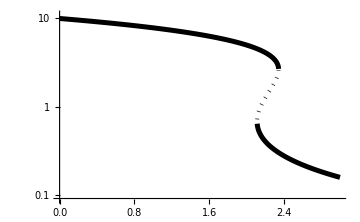

```mathematica
ListLogPlot[oneDT2,Joined->True,DataRange->{0,3},PlotStyle->{{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]}},PlotRange->{{0,3},{0.09,11}},LabelStyle->{14,GrayLevel[0]},ImageSize->Medium]
```

============== Old =============================

```mathematica
x1=x[1]/.solk3
```

{-1.18411×10^-17 (-1.84932×10^17+2.00263×10^14 k[3])+((1.47724×10^-76-2.55865×10^-76 ⅈ) (-1.51501×10^130+1.29319×10^128 k[3]-1.10121×10^124 k[3]^2))/(3.91457×10^162-4.19282×10^160 k[3]+4.54943×10^157 k[3]^2-2.58271×10^153 k[3]^3+1.32286×10^99 √(-1.16888×10^126+6.65861×10^124 k[3]-9.83065×10^122 k[3]^2+4.35082×10^120 k[3]^3-2.86213×10^116 k[3]^4))^(1/3)-(8.64182×10^-55+1.49681×10^-54 ⅈ) (3.91457×10^162-4.19282×10^160 k[3]+4.54943×10^157 k[3]^2-2.58271×10^153 k[3]^3+1.32286×10^99 √(-1.16888×10^126+6.65861×10^124 k[3]-9.83065×10^122 k[3]^2+4.35082×10^120 k[3]^3-2.86213×10^116 k[3]^4))^(1/3),-1.18411×10^-17 (-1.84932×10^17+2.00263×10^14 k[3])+((1.47724×10^-76+2.55865×10^-76 ⅈ) (-1.51501×10^130+1.29319×10^128 k[3]-1.10121×10^124 k[3]^2))/(3.91457×10^162-4.19282×10^160 k[3]+4.54943×10^157 k[3]^2-2.58271×10^153 k[3]^3+1.32286×10^99 √(-1.16888×10^126+6.65861×10^124 k[3]-9.83065×10^122 k[3]^2+4.35082×10^120 k[3]^3-2.86213×10^116 k[3]^4))^(1/3)-(8.64182×10^-55-1.49681×10^-54 ⅈ) (3.91457×10^162-4.19282×10^160 k[3]+4.54943×10^157 k[3]^2-2.58271×10^153 k[3]^3+1.32286×10^99 √(-1.16888×10^126+6.65861×10^124 k[3]-9.83065×10^122 k[3]^2+4.35082×10^120 k[3]^3-2.86213×10^116 k[3]^4))^(1/3),-1.18411×10^-17 (-1.84932×10^17+2.00263×10^14 k[3])-(2.95448×10^-76 (-1.51501×10^130+1.29319×10^128 k[3]-1.10121×10^124 k[3]^2))/(3.91457×10^162-4.19282×10^160 k[3]+4.54943×10^157 k[3]^2-2.58271×10^153 k[3]^3+1.32286×10^99 √(-1.16888×10^126+6.65861×10^124 k[3]-9.83065×10^122 k[3]^2+4.35082×10^120 k[3]^3-2.86213×10^116 k[3]^4))^(1/3)+1.72836×10^-54 (3.91457×10^162-4.19282×10^160 k[3]+4.54943×10^157 k[3]^2-2.58271×10^153 k[3]^3+1.32286×10^99 √(-1.16888×10^126+6.65861×10^124 k[3]-9.83065×10^122 k[3]^2+4.35082×10^120 k[3]^3-2.86213×10^116 k[3]^4))^(1/3)}

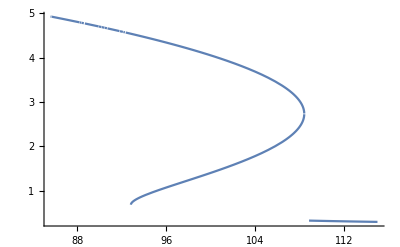

```mathematica
Plot[x1,{k[3],85,115},PlotRange->All]
```

```mathematica
k3=k[3]/.solk3[[1]]
```

-(0.000517581 (-1.37067×10^26-1.20797×10^28 x[1]-8.99411×10^27 x[1]^2+1.36909×10^27 x[1]^3))/(-1.54349×10^22+1.18303×10^23 x[1]+5.04111×10^21 x[1]^2)

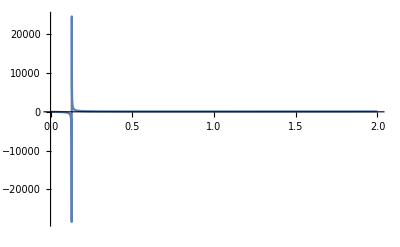

```mathematica
Plot[k3,{x[1],0,2},PlotRange->All]
```

#### Solve k[3]

```mathematica
{ssEqns[[2]],ssEqns[[3]]}==0
```

{-2.3574 x[2]+k[3] x[5]+0.264416 x[6],-0.0131009 x[3]-86.7794 x[1] x[3]+0.784202 x[4]+3.58304 x[5]+k[3] x[5]}==0

```mathematica
sol1=Solve[{ssEqns[[1]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],cons[[2]]}==0,{x[1],x[3],x[4],x[5],x[6]}]
```

{{x[1]→(0.5 (-1.75919×10^96-1.90705×10^96 k[3]+1.23016×10^97 x[2]+2.65648×10^93 k[3] x[2]-1. √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2)))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]),x[3]→(-2.99676×10^157+1.65566×10^157 k[3]+5.41697×10^157 k[3]^2+(4.17804×10^253)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.06645×10^253 k[3])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(7.34663×10^253 k[3]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.13089×10^252 k[3]^3)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+2.12587×10^158 x[2]-3.5038×10^158 k[3] x[2]-7.5447×10^154 k[3]^2 x[2]-(4.69806×10^254 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(5.54219×10^254 k[3] x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(3.23492×10^254 k[3]^2 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(2.96828×10^249 k[3]^3 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(1.24223×10^255 x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.99714×10^255 k[3] x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(4.3133×10^251 k[3]^2 x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(2.37498×10^157 √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(3.74927×10^157 k[3] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.11737×10^156 k[3]^2 √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.00981×10^158 x[2] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(1.62369×10^158 k[3] x[2] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]))/(-1.4419×10^157+7.96623×10^156 k[3]+2.60639×10^157 k[3]^2),x[4]→(-1.80231×10^157+9.95743×10^156 k[3]+3.25786×10^157 k[3]^2-(8.47185×10^254)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.00911×10^255 k[3])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.0027×10^254 k[3]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.09117×10^252 k[3]^3)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-1.65034×10^159 x[2]+2.64587×10^159 k[3] x[2]-7.40404×10^154 k[3]^2 x[2]+(9.52631×10^255 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(4.82085×10^255 k[3] x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(3.175×10^254 k[3]^2 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(2.91294×10^249 k[3]^3 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.51889×10^256 x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.9656×10^255 k[3] x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(4.23289×10^251 k[3]^2 x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(4.81578×10^158 √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(5.15667×10^157 k[3] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.09654×10^156 k[3]^2 √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(2.04761×10^159 x[2] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(1.59342×10^158 k[3] x[2] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]))/(-5.19084×10^158+2.86784×10^158 k[3]+9.38299×10^158 k[3]^2),x[5]→((8.55914×10^229)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(9.52902×10^229 k[3])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(2.71492×10^228 k[3]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+1.79142×10^134 x[2]-2.88108×10^134 k[3] x[2]-(9.62447×10^230 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(4.12156×10^230 k[3] x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(3.78182×10^225 k[3]^2 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(2.54484×10^231 x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(5.49548×10^227 k[3] x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(4.8654×10^133 √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(1.42362×10^132 k[3] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.06871×10^134 x[2] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]))/(6.76336×10^133-3.73663×10^133 k[3]-1.22255×10^134 k[3]^2),x[6]→(-(9.35737×10^214)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.9133×10^231 k[3])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(3.24342×10^231 k[3]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(9.24086×10^229 k[3]^3)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+5.4269×10^135 x[2]-9.09578×10^135 k[3] x[2]-3.27184×10^132 k[3]^2 x[2]+(1.0522×10^216 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(3.27591×10^232 k[3] x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(1.40287×10^232 k[3]^2 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(1.28723×10^227 k[3]^3 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.78218×10^216 x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(8.66196×10^232 k[3] x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.87051×10^229 k[3]^2 x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(5.31915×10^118 √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.65605×10^135 k[3] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(4.84562×10^133 k[3]^2 √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(2.26164×10^119 x[2] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(7.04132×10^135 k[3] x[2] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]))/(6.08702×10^134-3.36297×10^134 k[3]-1.10029×10^135 k[3]^2)},{x[1]→(0.5 (-1.75919×10^96-1.90705×10^96 k[3]+1.23016×10^97 x[2]+2.65648×10^93 k[3] x[2]+√(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2)))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]),x[3]→(-2.99676×10^157+1.65566×10^157 k[3]+5.41697×10^157 k[3]^2+(4.17804×10^253)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.06645×10^253 k[3])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(7.34663×10^253 k[3]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.13089×10^252 k[3]^3)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+2.12587×10^158 x[2]-3.5038×10^158 k[3] x[2]-7.5447×10^154 k[3]^2 x[2]-(4.69806×10^254 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(5.54219×10^254 k[3] x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(3.23492×10^254 k[3]^2 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(2.96828×10^249 k[3]^3 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(1.24223×10^255 x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.99714×10^255 k[3] x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(4.3133×10^251 k[3]^2 x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.37498×10^157 √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(3.74927×10^157 k[3] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(1.11737×10^156 k[3]^2 √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(1.00981×10^158 x[2] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.62369×10^158 k[3] x[2] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]))/(-1.4419×10^157+7.96623×10^156 k[3]+2.60639×10^157 k[3]^2),x[4]→(-1.80231×10^157+9.95743×10^156 k[3]+3.25786×10^157 k[3]^2-(8.47185×10^254)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.00911×10^255 k[3])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.0027×10^254 k[3]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.09117×10^252 k[3]^3)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-1.65034×10^159 x[2]+2.64587×10^159 k[3] x[2]-7.40404×10^154 k[3]^2 x[2]+(9.52631×10^255 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(4.82085×10^255 k[3] x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(3.175×10^254 k[3]^2 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(2.91294×10^249 k[3]^3 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.51889×10^256 x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.9656×10^255 k[3] x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(4.23289×10^251 k[3]^2 x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(4.81578×10^158 √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(5.15667×10^157 k[3] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(1.09654×10^156 k[3]^2 √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.04761×10^159 x[2] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.59342×10^158 k[3] x[2] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]))/(-5.19084×10^158+2.86784×10^158 k[3]+9.38299×10^158 k[3]^2),x[5]→((8.55914×10^229)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(9.52902×10^229 k[3])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(2.71492×10^228 k[3]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+1.79142×10^134 x[2]-2.88108×10^134 k[3] x[2]-(9.62447×10^230 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(4.12156×10^230 k[3] x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(3.78182×10^225 k[3]^2 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(2.54484×10^231 x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(5.49548×10^227 k[3] x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(4.8654×10^133 √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.42362×10^132 k[3] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(2.06871×10^134 x[2] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]))/(6.76336×10^133-3.73663×10^133 k[3]-1.22255×10^134 k[3]^2),x[6]→(-(9.35737×10^214)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.9133×10^231 k[3])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(3.24342×10^231 k[3]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(9.24086×10^229 k[3]^3)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+5.4269×10^135 x[2]-9.09578×10^135 k[3] x[2]-3.27184×10^132 k[3]^2 x[2]+(1.0522×10^216 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(3.27591×10^232 k[3] x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(1.40287×10^232 k[3]^2 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(1.28723×10^227 k[3]^3 x[2])/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.78218×10^216 x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(8.66196×10^232 k[3] x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(1.87051×10^229 k[3]^2 x[2]^2)/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(5.31915×10^118 √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(1.65605×10^135 k[3] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])+(4.84562×10^133 k[3]^2 √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(2.26164×10^119 x[2] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2])-(7.04132×10^135 k[3] x[2] √(-4. (2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]) (-1.14546×10^95 x[2]-2.49214×10^94 k[3] x[2])+(1.75919×10^96+1.90705×10^96 k[3]-1.23016×10^97 x[2]-2.65648×10^93 k[3] x[2])^2))/(2.68916×10^96+7.86852×10^94 k[3]-1.1434×10^97 x[2]))/(6.08702×10^134-3.36297×10^134 k[3]-1.10029×10^135 k[3]^2)}}

```mathematica
Solve[{ssEqns[[2]]}==0,{k[3]}]
```

{{k[3]→(2.3574 x[2]-0.264416 x[6])/x[5]}}

```mathematica
Solve[{{ssEqns[[1]],ssEqns[[4]],ssEqns[[5]],ssEqns[[3]],cons[[1]]}==0},{x[1],x[3],x[4],x[5],x[6]}]
```

{{x[1]→(0.5 (3.14983×10^79-1.40555×10^78 k[3]-3.36741×10^79 x[2]-9.86837×10^76 k[3] x[2]-1. √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2]))))/(3.37264×10^78+9.86837×10^76 k[3]),x[3]→(-1.20636×10^116-3.04116×10^115 k[3]-7.86564×10^113 k[3]^2+(1.90115×10^194)/(3.37264×10^78+9.86837×10^76 k[3])+(3.94432×10^193 k[3])/(3.37264×10^78+9.86837×10^76 k[3])-(8.99067×10^191 k[3]^2)/(3.37264×10^78+9.86837×10^76 k[3])-(5.53136×10^190 k[3]^3)/(3.37264×10^78+9.86837×10^76 k[3])+2.42416×10^116 x[2]+4.95287×10^115 k[3] x[2]-8.12768×10^113 k[3]^2 x[2]-(3.92174×10^194 x[2])/(3.37264×10^78+9.86837×10^76 k[3])-(8.98463×10^193 k[3] x[2])/(3.37264×10^78+9.86837×10^76 k[3])-(6.00088×10^191 k[3]^2 x[2])/(3.37264×10^78+9.86837×10^76 k[3])+(4.95391×10^190 k[3]^3 x[2])/(3.37264×10^78+9.86837×10^76 k[3])-1.19774×10^116 x[2]^2-2.62904×10^115 k[3] x[2]^2-7.60168×10^112 k[3]^2 x[2]^2+(2.01977×10^194 x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])+(5.02439×10^193 k[3] x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])+(1.42541×10^192 k[3]^2 x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])+(3.75081×10^189 k[3]^3 x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])-(6.03572×10^114 √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])-(1.52157×10^114 k[3] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])-(3.93537×10^112 k[3]^2 √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])+(5.99799×10^114 x[2] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])+(1.47449×10^114 k[3] x[2] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])+(3.80084×10^112 k[3]^2 x[2] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3]))/(1.48189×10^116-3.99794×10^116 k[3]-6.07546×10^116 k[3]^2-1.84919×10^116 x[2]+6.83246×10^116 k[3] x[2]+6.09048×10^115 k[3]^2 x[2]),x[4]→(-1.89599×10^126-2.1125×10^126 k[3]-6.01888×10^124 k[3]^2+(2.98795×10^204)/(3.37264×10^78+9.86837×10^76 k[3])+(3.19583×10^204 k[3])/(3.37264×10^78+9.86837×10^76 k[3])-(5.37042×10^202 k[3]^2)/(3.37264×10^78+9.86837×10^76 k[3])-(4.23266×10^201 k[3]^3)/(3.37264×10^78+9.86837×10^76 k[3])+4.26066×10^126 x[2]+2.33591×10^126 k[3] x[2]+1.20722×10^124 k[3]^2 x[2]-(6.92367×10^204 x[2])/(3.37264×10^78+9.86837×10^76 k[3])-(3.83559×10^204 k[3] x[2])/(3.37264×10^78+9.86837×10^76 k[3])-(1.01983×10^203 k[3]^2 x[2])/(3.37264×10^78+9.86837×10^76 k[3])+(1.26365×10^200 k[3]^3 x[2])/(3.37264×10^78+9.86837×10^76 k[3])-2.36429×10^126 x[2]^2-2.12579×10^125 k[3] x[2]^2-6.02668×10^122 k[3]^2 x[2]^2+(3.98694×10^204 x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])+(4.75134×10^203 k[3] x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])+(1.15053×10^202 k[3]^2 x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])+(2.97368×10^199 k[3]^3 x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])-(9.48607×10^124 √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])-(1.05694×10^125 k[3] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])-(3.01139×10^123 k[3]^2 √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])+(1.18398×10^125 x[2] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])+(1.37628×10^124 k[3] x[2] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])+(3.01334×10^122 k[3]^2 x[2] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3]))/(-1.43019×10^125+3.85847×10^125 k[3]+5.86352×10^125 k[3]^2+1.78468×10^125 x[2]-6.59411×10^125 k[3] x[2]-5.87801×10^124 k[3]^2 x[2]),x[5]→(1.30097×10^32-(2.05025×10^110)/(3.37264×10^78+9.86837×10^76 k[3])+(9.14884×10^108 k[3])/(3.37264×10^78+9.86837×10^76 k[3])-1.29082×10^32 x[2]+(2.19187×10^110 x[2])/(3.37264×10^78+9.86837×10^76 k[3])+(6.4234×10^107 k[3] x[2])/(3.37264×10^78+9.86837×10^76 k[3])+(6.50908×10^30 √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3]))/(1.30182×10^31-4.92337×10^31 k[3]),x[6]→(4.92018×10^32 k[3]-(7.75387×10^110 k[3])/(3.37264×10^78+9.86837×10^76 k[3])+(3.46002×10^109 k[3]^2)/(3.37264×10^78+9.86837×10^76 k[3])-1.16064×10^32 x[2]-4.92337×10^31 k[3] x[2]+(8.2895×10^110 k[3] x[2])/(3.37264×10^78+9.86837×10^76 k[3])+(2.42928×10^108 k[3]^2 x[2])/(3.37264×10^78+9.86837×10^76 k[3])+(2.46168×10^31 k[3] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3]))/(-1.30182×10^31+4.92337×10^31 k[3])},{x[1]→(0.5 (3.14983×10^79-1.40555×10^78 k[3]-3.36741×10^79 x[2]-9.86837×10^76 k[3] x[2]+√((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2]))))/(3.37264×10^78+9.86837×10^76 k[3]),x[3]→(-1.20636×10^116-3.04116×10^115 k[3]-7.86564×10^113 k[3]^2+(1.90115×10^194)/(3.37264×10^78+9.86837×10^76 k[3])+(3.94432×10^193 k[3])/(3.37264×10^78+9.86837×10^76 k[3])-(8.99067×10^191 k[3]^2)/(3.37264×10^78+9.86837×10^76 k[3])-(5.53136×10^190 k[3]^3)/(3.37264×10^78+9.86837×10^76 k[3])+2.42416×10^116 x[2]+4.95287×10^115 k[3] x[2]-8.12768×10^113 k[3]^2 x[2]-(3.92174×10^194 x[2])/(3.37264×10^78+9.86837×10^76 k[3])-(8.98463×10^193 k[3] x[2])/(3.37264×10^78+9.86837×10^76 k[3])-(6.00088×10^191 k[3]^2 x[2])/(3.37264×10^78+9.86837×10^76 k[3])+(4.95391×10^190 k[3]^3 x[2])/(3.37264×10^78+9.86837×10^76 k[3])-1.19774×10^116 x[2]^2-2.62904×10^115 k[3] x[2]^2-7.60168×10^112 k[3]^2 x[2]^2+(2.01977×10^194 x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])+(5.02439×10^193 k[3] x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])+(1.42541×10^192 k[3]^2 x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])+(3.75081×10^189 k[3]^3 x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])+(6.03572×10^114 √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])+(1.52157×10^114 k[3] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])+(3.93537×10^112 k[3]^2 √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])-(5.99799×10^114 x[2] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])-(1.47449×10^114 k[3] x[2] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])-(3.80084×10^112 k[3]^2 x[2] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3]))/(1.48189×10^116-3.99794×10^116 k[3]-6.07546×10^116 k[3]^2-1.84919×10^116 x[2]+6.83246×10^116 k[3] x[2]+6.09048×10^115 k[3]^2 x[2]),x[4]→(-1.89599×10^126-2.1125×10^126 k[3]-6.01888×10^124 k[3]^2+(2.98795×10^204)/(3.37264×10^78+9.86837×10^76 k[3])+(3.19583×10^204 k[3])/(3.37264×10^78+9.86837×10^76 k[3])-(5.37042×10^202 k[3]^2)/(3.37264×10^78+9.86837×10^76 k[3])-(4.23266×10^201 k[3]^3)/(3.37264×10^78+9.86837×10^76 k[3])+4.26066×10^126 x[2]+2.33591×10^126 k[3] x[2]+1.20722×10^124 k[3]^2 x[2]-(6.92367×10^204 x[2])/(3.37264×10^78+9.86837×10^76 k[3])-(3.83559×10^204 k[3] x[2])/(3.37264×10^78+9.86837×10^76 k[3])-(1.01983×10^203 k[3]^2 x[2])/(3.37264×10^78+9.86837×10^76 k[3])+(1.26365×10^200 k[3]^3 x[2])/(3.37264×10^78+9.86837×10^76 k[3])-2.36429×10^126 x[2]^2-2.12579×10^125 k[3] x[2]^2-6.02668×10^122 k[3]^2 x[2]^2+(3.98694×10^204 x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])+(4.75134×10^203 k[3] x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])+(1.15053×10^202 k[3]^2 x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])+(2.97368×10^199 k[3]^3 x[2]^2)/(3.37264×10^78+9.86837×10^76 k[3])+(9.48607×10^124 √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])+(1.05694×10^125 k[3] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])+(3.01139×10^123 k[3]^2 √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])-(1.18398×10^125 x[2] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])-(1.37628×10^124 k[3] x[2] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3])-(3.01334×10^122 k[3]^2 x[2] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3]))/(-1.43019×10^125+3.85847×10^125 k[3]+5.86352×10^125 k[3]^2+1.78468×10^125 x[2]-6.59411×10^125 k[3] x[2]-5.87801×10^124 k[3]^2 x[2]),x[5]→(1.30097×10^32-(2.05025×10^110)/(3.37264×10^78+9.86837×10^76 k[3])+(9.14884×10^108 k[3])/(3.37264×10^78+9.86837×10^76 k[3])-1.29082×10^32 x[2]+(2.19187×10^110 x[2])/(3.37264×10^78+9.86837×10^76 k[3])+(6.4234×10^107 k[3] x[2])/(3.37264×10^78+9.86837×10^76 k[3])-(6.50908×10^30 √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3]))/(1.30182×10^31-4.92337×10^31 k[3]),x[6]→(4.92018×10^32 k[3]-(7.75387×10^110 k[3])/(3.37264×10^78+9.86837×10^76 k[3])+(3.46002×10^109 k[3]^2)/(3.37264×10^78+9.86837×10^76 k[3])-1.16064×10^32 x[2]-4.92337×10^31 k[3] x[2]+(8.2895×10^110 k[3] x[2])/(3.37264×10^78+9.86837×10^76 k[3])+(2.42928×10^108 k[3]^2 x[2])/(3.37264×10^78+9.86837×10^76 k[3])-(2.46168×10^31 k[3] √((-3.14983×10^79+1.40555×10^78 k[3]+3.36741×10^79 x[2]+9.86837×10^76 k[3] x[2])^2-4. (3.37264×10^78+9.86837×10^76 k[3]) (-2.20487×10^79-2.3902×10^79 k[3]+2.75138×10^79 x[2]+2.39611×10^78 k[3] x[2])))/(3.37264×10^78+9.86837×10^76 k[3]))/(-1.30182×10^31+4.92337×10^31 k[3])}}

```mathematica
Solve[ssEqns[[6]]==0,x[6]]
```

{{x[6]→-3.34744 (-1.19999 x[1] x[4]-1.04135 x[5])}}

#### Solve x[2]

```mathematica
solution=NSolve[{{ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],cons[[2]]}==0},{x[1],x[3],x[4],x[5],x[6]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x[1]→(1.32856×10^-38 (-1.13253×10^86 T[2]+1.67937×10^85 x[2]-1. √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2)))/(1.68198×10^47 T[2]-4.06607×10^47 x[2]),x[3]→1.09291×10^-139 (8.99952×10^138 T[2]-(7.56707×10^185 T[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-1.33838×10^138 x[2]+(1.94149×10^186 T[2] x[2])/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-(2.71256×10^185 x[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-(6.68156×10^99 T[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+(1.61522×10^100 x[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])),x[4]→9.83621×10^-139 (1.67052×10^136 T[2]-(2.62681×10^183 T[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+3.04925×10^136 x[2]+(6.73963×10^183 T[2] x[2])/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-(9.41628×10^182 x[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-(2.31941×10^97 T[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+(5.60702×10^97 x[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])),x[5]→5.82502×10^-117 (-(4.18177×10^160 T[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+4.31451×10^114 x[2]+(1.07292×10^161 T[2] x[2])/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-(1.49903×10^160 x[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-(3.69241×10^74 T[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+(8.92615×10^74 x[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])),x[6]→1.74751×10^-116 ((4.89433×10^162 T[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+5.21589×10^114 x[2]-(1.25575×10^163 T[2] x[2])/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+(1.75446×10^162 x[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+(4.32159×10^76 T[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-(1.04471×10^77 x[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2]))},{x[1]→(1.32856×10^-38 (-1.13253×10^86 T[2]+1.67937×10^85 x[2]+√(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2)))/(1.68198×10^47 T[2]-4.06607×10^47 x[2]),x[3]→1.09291×10^-139 (8.99952×10^138 T[2]-(7.56707×10^185 T[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-1.33838×10^138 x[2]+(1.94149×10^186 T[2] x[2])/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-(2.71256×10^185 x[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+(6.68156×10^99 T[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-(1.61522×10^100 x[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])),x[4]→9.83621×10^-139 (1.67052×10^136 T[2]-(2.62681×10^183 T[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+3.04925×10^136 x[2]+(6.73963×10^183 T[2] x[2])/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-(9.41628×10^182 x[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+(2.31941×10^97 T[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-(5.60702×10^97 x[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])),x[5]→5.82502×10^-117 (-(4.18177×10^160 T[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+4.31451×10^114 x[2]+(1.07292×10^161 T[2] x[2])/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-(1.49903×10^160 x[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+(3.69241×10^74 T[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-(8.92615×10^74 x[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])),x[6]→1.74751×10^-116 ((4.89433×10^162 T[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+5.21589×10^114 x[2]-(1.25575×10^163 T[2] x[2])/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+(1.75446×10^162 x[2]^2)/(1.68198×10^47 T[2]-4.06607×10^47 x[2])-(4.32159×10^76 T[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])+(1.04471×10^77 x[2] √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))/(1.68198×10^47 T[2]-4.06607×10^47 x[2]))}}

```mathematica
polyx21=Simplify[cons[[1]]/.solution[[1]]]
```

(8.52852×10^46 T[2]^2-4.23315×10^47 x[2]^2-1.32856×10^-38 √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2)+x[2] (4.28655×10^48-1.82045×10^-39 √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))+T[2] (-3.18553×10^48-3.10613×10^46 x[2]+7.5305×10^-40 √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2)))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])

```mathematica
polyx22=Simplify[cons[[1]]/.solution[[2]]]
```

(8.52852×10^46 T[2]^2-4.23315×10^47 x[2]^2+1.32856×10^-38 √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2)+T[2] (-3.18553×10^48-3.10613×10^46 x[2]-7.5305×10^-40 √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2))+x[2] (4.28655×10^48+1.82045×10^-39 √(1.28262×10^172 T[2]^2-3.72159×10^171 T[2] x[2]+8.31064×10^169 x[2]^2)))/(1.68198×10^47 T[2]-4.06607×10^47 x[2])

```mathematica
solx21=Solve[polyx21==0,{x[2]}];
```

```mathematica
solx22=Solve[polyx22==0,{x[2]}];
```

```mathematica
x21=x[2]/.solx21;
```

```mathematica
x22=x[2]/.solx22;
```

```mathematica
Length[x21]
```

4

```mathematica
Length[x22]
```

4

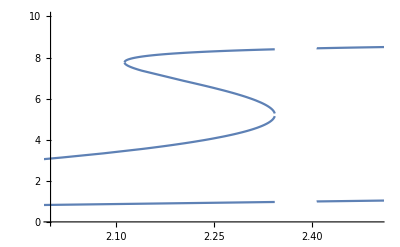

```mathematica
Plot[x21,{T[2],0,3},PlotRange->{{2.0,2.5},{0,10}}]
```

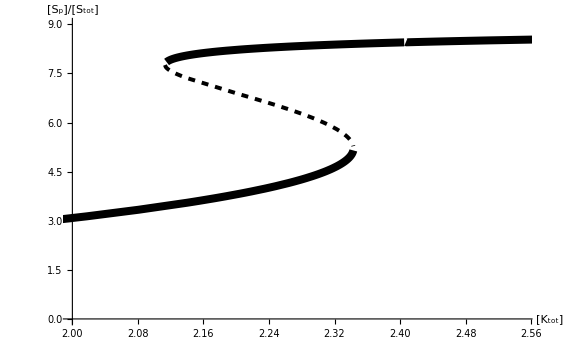

```mathematica
Plot[{ConditionalExpression[x22[[2]],0<T[2]<3],ConditionalExpression[x22[[3]],0<T[2]<3],ConditionalExpression[Re[x22[[4]]],2.115<T[2]<2.405]},{T[2],0,3},PlotRange->{{2,2.55},{0,9}},PlotStyle->{{Black,Thickness[0.01]},{Dashed,Black,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Thickness[0.01]}},TicksStyle->Automatic,AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["K","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]","/","[",SubscriptBox["S","tot"],"]"}]]},LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

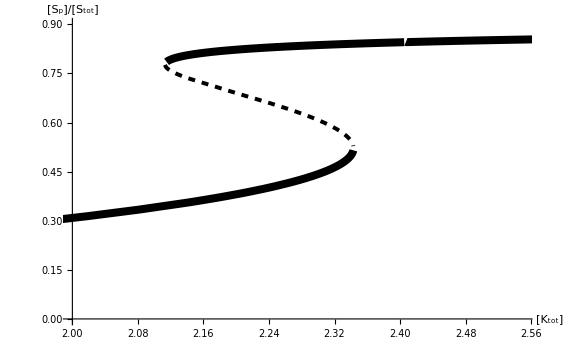

```mathematica
Plot[{ConditionalExpression[x22[[2]]/T[1],0<T[2]<3],ConditionalExpression[x22[[3]]/T[1],0<T[2]<3],ConditionalExpression[Re[x22[[4]]]/T[1],2.115<T[2]<2.405]},{T[2],0,3},PlotRange->{{2,2.55},{0,0.9}},PlotStyle->{{Black,Thickness[0.01]},{Dashed,Black,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Thickness[0.01]}},TicksStyle->Automatic,AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["K","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]","/","[",SubscriptBox["S","tot"],"]"}]]},LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

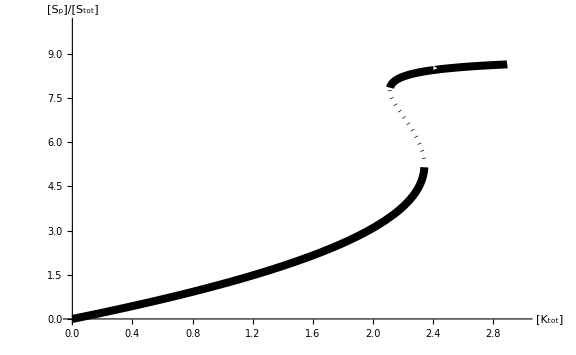

```mathematica
Plot[{ConditionalExpression[x22[[2]],0<T[2]<3],ConditionalExpression[x22[[3]],2<T[2]<2.5],ConditionalExpression[Re[x22[[4]]],2.115<T[2]<2.405]},{T[2],0,3},PlotRange->{{0,3},{0,10}},PlotStyle->{{Black,Thickness[0.01]},{Dotted,Black,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Thickness[0.01]}},TicksStyle->Automatic,AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["K","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]","/","[",SubscriptBox["S","tot"],"]"}]]},LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

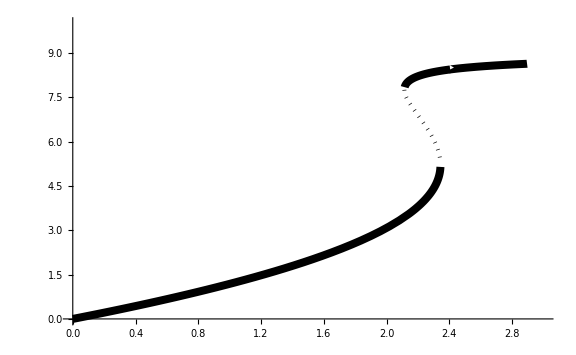

```mathematica
Plot[{ConditionalExpression[x22[[2]],0<T[2]<3],ConditionalExpression[x22[[3]],2<T[2]<2.5],ConditionalExpression[Re[x22[[4]]],2.115<T[2]<2.405]},{T[2],0,3},PlotRange->{{0,3},{0,10}},PlotStyle->{{Black,Thickness[0.01]},{Dotted,Black,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Thickness[0.01]}},TicksStyle->Automatic,(*AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["K","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]","/","[",SubscriptBox["S","tot"],"]"}]]},*)LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

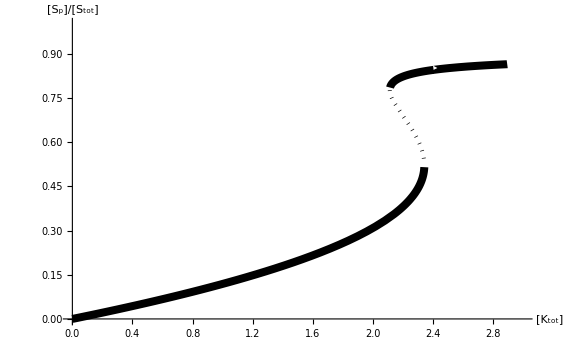

```mathematica
Plot[{ConditionalExpression[x22[[2]]/T[1],0<T[2]<3],ConditionalExpression[x22[[3]]/T[1],2<T[2]<2.5],ConditionalExpression[Re[x22[[4]]]/T[1],2.115<T[2]<2.405]},{T[2],0,3},PlotRange->{{0,3},{0,1}},PlotStyle->{{Black,Thickness[0.01]},{Dotted,Black,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Thickness[0.01]}},TicksStyle->Automatic,AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["K","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]","/","[",SubscriptBox["S","tot"],"]"}]]},LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

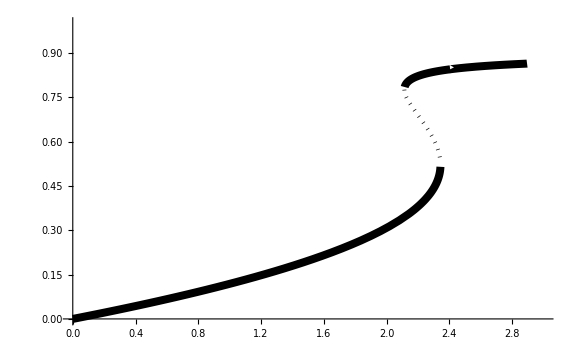

```mathematica
Plot[{ConditionalExpression[x22[[2]]/T[1],0<T[2]<3],ConditionalExpression[x22[[3]]/T[1],2<T[2]<2.5],ConditionalExpression[Re[x22[[4]]]/T[1],2.115<T[2]<2.405]},{T[2],0,3},PlotRange->{{0,3},{0,1}},PlotStyle->{{Black,Thickness[0.01]},{Dotted,Black,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Thickness[0.01]}},TicksStyle->Automatic,(*AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["K","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]","/","[",SubscriptBox["S","tot"],"]"}]]},*)LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

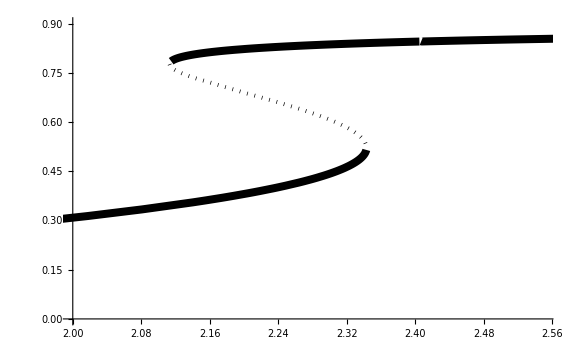

```mathematica
Plot[{ConditionalExpression[x22[[2]]/T[1],0<T[2]<3],ConditionalExpression[x22[[3]]/T[1],0<T[2]<3],ConditionalExpression[Re[x22[[4]]]/T[1],2.115<T[2]<2.405]},{T[2],0,3},PlotRange->{{2,2.55},{0,0.9}},PlotStyle->{{Black,Thickness[0.01]},{Dotted,Black,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Thickness[0.01]}},TicksStyle->Automatic,(*AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["K","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]","/","[",SubscriptBox["S","tot"],"]"}]]},*)LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

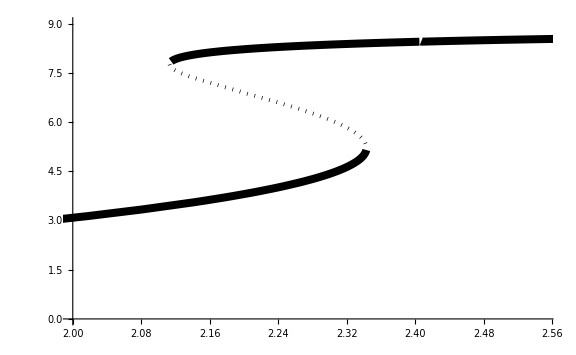

```mathematica
Plot[{ConditionalExpression[x22[[2]],0<T[2]<3],ConditionalExpression[x22[[3]],0<T[2]<3],ConditionalExpression[Re[x22[[4]]],2.115<T[2]<2.405]},{T[2],0,3},PlotRange->{{2,2.55},{0,9}},PlotStyle->{{Black,Thickness[0.01]},{Dotted,Black,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Thickness[0.01]}},TicksStyle->Automatic,(*AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["K","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]","/","[",SubscriptBox["S","tot"],"]"}]]},*)LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

```mathematica
x22/.{T[2]->2.38}
```

{0.984517+2.27485×10^-13 ⅈ,5.18666+0.751245 ⅈ,5.18666-0.751245 ⅈ,8.43121-3.73757×10^-13 ⅈ}

```mathematica
DeleteDuplicates[Re[{Sqrt[-5],Sqrt[-5]}]]
```

{0}